```mathematica
(* 完全な球体として計算 *)
SphereArcLength[{lat1_,lon1_},{lat2_,lon2_}]:=Module[{
a=6378137,
x1,y1,z1,x2,y2,z2,r},
x1=Cos[lat1 Degree]Cos[lon1 Degree];
y1=Cos[lat1 Degree] Sin[lon1 Degree];
z1=Sin[lat1 Degree];
x2=Cos[lat2 Degree]Cos[lon2 Degree];
y2=Cos[lat2 Degree] Sin[lon2 Degree];
z2=Sin[lat2 Degree];
r=EuclideanDistance[{x1,y1,z1},{x2,y2,z2}];
2a ArcSin[r/2]
]
```

```mathematica
(* ヒュベニの公式 *)
Hubeny[{lat1_,lon1_},{lat2_,lon2_}]:=Module[{
a=6378137,
b=6356752314245*^-6,
e,
rlat1=lat1 Degree,
rlon1=lon1 Degree,
rlat2=lat2 Degree,
rlon2=lon2 Degree,
latdiff,londiff,latave,w,m,n},
e=Sqrt[1-b^2/a^2];
latdiff=rlat1-rlat2;
londiff=rlon1-rlon2;
latave=(rlat1+rlat2)/2;
w=Sqrt[1-(Sin[latave]e)^2];
m=a(1-e^2)/w^3;
n=a/w;
Sqrt[(latdiff*m)^2+(londiff*n*Cos[latave])^2]
]
```

```mathematica
(* 国土地理院の測量計算サイトを呼び出して計算させる *)
(* http://surveycalc.gsi.go.jp/sokuchi/surveycalc/bl2stf.html *)
GeoDistanceGSINet[{lat1_,lon1_},{lat2_,lon2_}]:=Monitor[Module[{params={}},
params=Append[params,"select=0"];
params=Append[params,"ellipsoid=GRS80"];
params=Append[params,"latitude1="<>ToString@CForm[lat1]];
params=Append[params,"longitude1="<>ToString@CForm[lon1]];
params=Append[params,"latitude2="<>ToString@CForm[lat2]];
params=Append[params,"longitude2="<>ToString@CForm[lon2]];
params=Append[params,"tanni=1"];
params=Append[params,"outputType=json"];
ToExpression["geoLength"/.("OutputData"/.Import["http://surveycalc.gsi.go.jp/sokuchi/surveycalc/bl2st_calc.pl?"<>StringJoin[Riffle[params,"&"]],"JSON"])
]
],{lat1,lon1,lat2,lon2}]
```

```mathematica
(* http://surveycalc.gsi.go.jp/sokuchi/surveycalc/algorithm/bl2st/bl2st.htm *)
GeoDistanceGSI[{lat1_,lon1_},{lat2_,lon2_}]:=Catch[Module[{
a=6378137,
b=6356752314245*^-6,
f,
L,L2,Δ,Σ,u1,u2,Σ2,Δ2,ξ,ξ2,η,η2,x,y,c,ϵ,
θ,g,h,σ,J,K,γ,Γ,ζ,ζ2,D,E,F,G,
R,d1,d2,q,f1,γ0,A0,B0,ψ,j,k,j1,ψ2,ψ3,
n0,A,B,s
},
f=1-b/a;
L=(Mod[lon2-lon1+180,360]-180)Degree;
L2=Mod[180Degree-L+180Degree,360Degree]-180Degree;
Δ=(lat2-lat1)Degree;
Σ=(lat1+lat2)Degree;
u1=ArcTan[(1-f)Tan[lat1 Degree]];
u2=ArcTan[(1-f)Tan[lat2 Degree]];
Σ2=Mod[u1+u2+180Degree,360Degree]-180Degree;
Δ2=Mod[u2-u1+180Degree,360Degree]-180Degree;
ξ=Cos[Σ2/2];
ξ2=Sin[Σ2/2];
η=Sin[Δ2/2];
η2=Cos[Δ2/2];
x=Sin[u1]Sin[u2];
y=Cos[u1]Cos[u2];
c=y Cos[L]+x;
ϵ=f(2-f)/(1-f)^2;

Which[
TrueQ[c≥0],(* Zone 1 *)θ=L(1+f y),
TrueQ[0>c≥-Cos[3Degree Cos[u1]]],(* Zone 2 *)θ=L2,
True,(* Zone 3*)
R=f π Cos[u1]^2(1-(1/4)f(1+f)Sin[u1]^2+3f^2Sin[u1]^4/16);
d1=L2 Cos[u1]-R;
d2=Abs[Σ2]+R;
q=L2/(f π);
f1=f(1+f/2)/4;
γ0=q+f1 q-f1 q^3;
Which[
TrueQ[Σ≠0],
(* Zone 3a *)Print["Zone 3a"];
A0=ArcTan[d1/d2];
B0=ArcSin[R/Sqrt[d1^2+d2^2]];If[B0<0,Throw[-1]];
ψ=A0+B0;
j=γ0/Cos[u1];
k=(1+f1)Abs[Σ2](1-f y)/(f π y);
j1=j/(1+k Sec[ψ]);
ψ2=ArcSin[j1];
ψ3=ArcSin[j1 Cos[u1]/Cos[u2]];
θ=2 ArcTan[Tan[(ψ2+ψ3)/2]Sin[Abs[Σ2]/2]/Cos[Δ2/2]];,
True,
Which[
TrueQ[d1>0],
(* Zone 3b1 *)Print["Zone 3b1"];
θ=L2,
TrueQ[d1==0],
(* Zone 3b2 *)Print["Zone 3b2"];
Γ=Sin[u1]^2;
n0=ϵ Γ/(Sqrt[1+ϵ Γ]+1)^2;
A=(1+n0)(1+5n0^2/4);
s=(1-f)a A π;
Throw[s],
True,
(* Zone 3b3 *)Print["Zone 3b3"];
Module[{γn=γ0,m,n,w},
While[True,
γ=γn;
Γ=1-γ^2;
D=f(1+f)/f-3f^2Γ/16;
γn=q/(1-D Γ);
If[Abs[γn-γ]<1.0*^-15,Break[]]
];
m=1-q Sec[u1];
n=D Γ/(1-D Γ);
n0=ϵ Γ/(Sqrt[1+ϵ Γ]+1)^2;
A=(1+n0)(1+5n0^2/4);
s=(1-f)a A π;
Throw[s];
];
];
];
];
While[True,
Which[
TrueQ[c≥0],
g=Sqrt[η^2Cos[θ/2]^2+ξ^2Sin[θ/2]^2];
h=Sqrt[η2^2Cos[θ/2]^2+ξ2^2Sin[θ/2]^2];,
True,
g=Sqrt[η^2Sin[θ/2]^2+ξ^2Cos[θ/2]^2];
h=Sqrt[η2^2Sin[θ/2]^2+ξ2^2Cos[θ/2]^2];
];
σ=2ArcTan[g/h];
J=2g h;
K=h^2-g^2;
γ=y Sin[θ]/J;
Γ=1-γ^2;
ζ=Γ K-2x;
ζ2=ζ+x;
D=f(1+f)/4-3f^2Γ/16;
E=(1-D Γ)f γ(σ+D J(ζ+D K(2ζ^2-Γ^2)));

Which[
TrueQ[c≥0],F=θ-L-E,
True,F=θ-L2-E
];
G=f γ^2(1-2D Γ)+f ζ2(σ/J)(1-D Γ+f γ^2/2)+f^2ζ ζ2/4;
θ=θ-F/(1-G);
If[Abs[F]<1.0*^-15,Break[]];
];

n0=ϵ Γ/(Sqrt[1+ϵ Γ]+1)^2;
A=(1+n0)(1+5n0^2/4);
B=ϵ(1-3n0^2/8)/(Sqrt[1+ϵ Γ]+1)^2;
s=(1-f)a A(σ-B J(ζ-(1/4)B(K(Γ^2-2ζ^2)-B ζ(1-4K^2)(3Γ^2-4ζ^2)/6)));
Throw[s]
]];
```

```mathematica
(* GeographicLibをJLink経由で使って計算 *)
<<JLink`
InstallJava[];
AddToClassPath[FileNameJoin[{NotebookDirectory[],"GeographicLib"}]];
LoadJavaClass["net.sf.geographiclib.Geodesic",AllowShortContext->False];
wgs84=net`sf`geographiclib`Geodesic`WGS84;
GeoDistanceGeodesicLib[{lat1_,lon1_},{lat2_,lon2_}]:=Module[{result},
result=wgs84@Inverse[lat1,lon1,lat2,lon2];
result@s12
];
```

```mathematica
(* 確認 *)
NumberForm[#,{16,15}]&/@With[{
p1={RandomReal[{-90,90}],RandomReal[{-180,180}]},
p2={RandomReal[{-90,90}],RandomReal[{-180,180}]}
},
Print[{p1,p2}];
{
GeoDistance[p1,p2,"WGS84",Method->"ExtendedNewtonRaphson"],
SphereArcLength[p1,p2],
Hubeny[p1,p2],
GeoDistanceGSI[p1,p2],
GeoDistanceGSINet[p1,p2],
GeoDistanceGeodesicLib[p1,p2]
}
]//TableForm
```

{{-4.65656,114.356},{-33.7531,-117.222}}

1.313725540517432×10^7
1.313870510802373×10^7
2.456535883265659×10^7
1.308944160813860×10^7
1.313725545100000×10^7
1.313725545089443×10^7

```mathematica
methods={"GeographicLib","Vincenty75","Robbin61","ExtendedNewtonRaphson","Hubeny","測量計算サイト移植","Sphere"};
```

```mathematica
(* 地球上のランダムな2点の距離を計算 *)
points=Transpose[{RandomReal[{-90,90},#],RandomReal[{-180,180},#]}]&[1000];
dist0=MapThread[GeoDistanceGeodesicLib,{Most@points,Rest@points}];
dist1=MapThread[GeoDistance[#1,#2,"WGS84",Method->"Vincenty75"]&,{Most@points,Rest@points}];
dist2=MapThread[GeoDistance[#1,#2,"WGS84",Method->"Robbin61"]&,{Most@points,Rest@points}];
dist3=MapThread[GeoDistance[#1,#2,"WGS84",Method->"ExtendedNewtonRaphson"]&,{Most@points,Rest@points}];
dist4=MapThread[Hubeny,{Most@points,Rest@points}];
dist5=MapThread[GeoDistanceGSI,{Most@points,Rest@points}];
dist6=MapThread[SphereArcLength,{Most@points,Rest@points}];
err1=Abs[dist1/dist0-1];
err2=Abs[dist2/dist0-1];
err3=Abs[dist3/dist0-1];
err4=Abs[dist4/dist0-1];
err5=Abs[dist5/dist0-1];
err6=Abs[dist6/dist0-1];
```

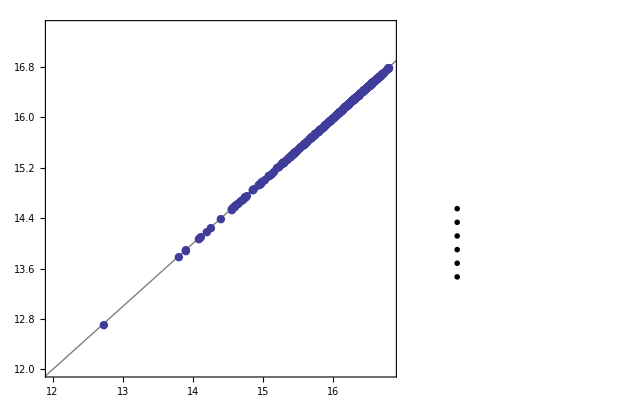

```mathematica
Needs["PlotLegends`"]
graph1=ListLogLogPlot[{
Transpose[{dist0,dist1}],
Transpose[{dist0,dist2}],
Transpose[{dist0,dist3}],
Transpose[{dist0,dist4}],
Transpose[{dist0,dist5}],
Transpose[{dist0,dist6}]
},
Frame->True,
FrameLabel->{"True Distance (m)","Calculated Distance (m)"},
FrameTicks->{{1.*^6,2.*^6,5.*^6,1.*^7,2.*^7},{1.*^6,2.*^6,5.*^6,1.*^7,2.*^7},None,None},
PlotRange->{Full,Full},
PlotMarkers->{"●","■","◆","▲","▼","○"},
PlotLegend->Rest@methods,
LegendPosition->{1.1,-0.4},
LegendShadow->None,
LegendSize->{1,0.5},
LegendTextSpace->5,
ImageSize->640,
AspectRatio->1,
Prolog->{Gray,Line[{{1,1},{2*^7,2*^7}}]}
]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"hubeny_graph001.png"}],graph1];
```

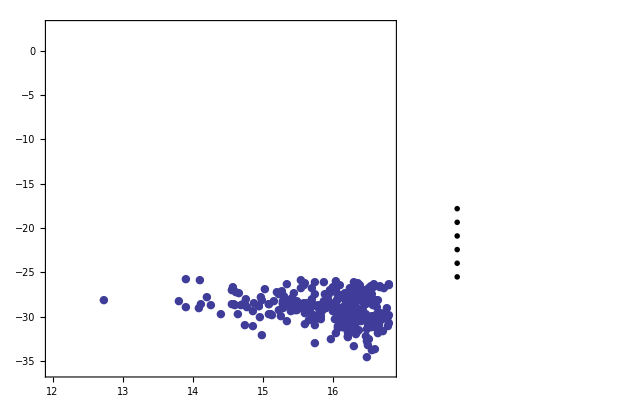

```mathematica
graph2=ListLogLogPlot[{
Transpose[{dist0,err1}],
Transpose[{dist0,err2}],
Transpose[{dist0,err3}],
Transpose[{dist0,err4}],
Transpose[{dist0,err5}],
Transpose[{dist0,err6}]
},
Frame->True,
FrameLabel->{"True Distance (m)","Error"},
FrameTicks->{{1.*^6,2.*^6,5.*^6,1.*^7,2.*^7},Automatic,None,None},
PlotRange->{Full,Full},
PlotMarkers->{"●","■","◆","▲","▼","○"},
PlotLegend->Rest@methods,
LegendPosition->{1.1,-0.4},
LegendShadow->None,
LegendSize->{1,0.5},
LegendTextSpace->5,
ImageSize->640,
AspectRatio->1,
Prolog->{Gray,Line[{{1,1},{2*^7,2*^7}}]}
]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"hubeny_graph002.png"}],graph2];
```

```mathematica
TableForm[ScientificForm[Max@#,{16,3},NumberPadding->{"","0"}]&/@{err1,err2,err3,err4,err5,err6},TableHeadings->{Rest@methods}]
```

Vincenty75 | 7.137×10^-12
Robbin61 | 9.879×10^-1
ExtendedNewtonRaphson | 1.404×10^-6
Hubeny | 1.417×10^1
測量計算サイト移植 | 6.675×10^-3
Sphere | 6.260×10^-3

```mathematica
(* 枕崎から稚内までのルートの道のりを計算(400点) *)
path=Import[FileNameJoin[{NotebookDirectory[],"makurazaki_wakkanai_reduced.gpx"}],{"Data",1,"Geometry",1}][[1,1]];
Dimensions[path]
```

{400,2}

```mathematica
Print[Timing[total0=Total[GeoDistanceGeodesicLib@@@Partition[path,2, 1]];]];Print[Timing[total1=Total[GeoDistance[#1,#2,"WGS84",Method->"Vincenty75"]&@@@Partition[path,2, 1]];]];
Print[Timing[total2=Total[GeoDistance[#1,#2,"WGS84",Method->"Robbin61"]&@@@Partition[path,2, 1]];]];
Print[Timing[total3=Total[GeoDistance[#1,#2,"WGS84",Method->"ExtendedNewtonRaphson"]&@@@Partition[path,2, 1]];]];
Print[Timing[total4=Total[Hubeny@@@Partition[path,2, 1]];]];
Print[Timing[total5=Total[GeoDistanceGSI@@@Partition[path,2, 1]];]];
Print[Timing[total6=Total[SphereArcLength@@@Partition[path,2, 1]];]];
```

{0.212013,Null}

{0.504031,Null}

{0.672042,Null}

{0.520033,Null}

{0.152009,Null}

{0.124008,Null}

{0.012001,Null}

```mathematica
TableForm[NumberForm[#,{16,15}]&/@{
total0,total1,total2,total3,total4,total5,total6
},TableHeadings->{methods}]
```

GeographicLib | 2.541657039259448×10^6
Vincenty75 | 2.541657039264922×10^6
Robbin61 | 2.538452677040755×10^6
ExtendedNewtonRaphson | 2.541656533178208×10^6
Hubeny | 2.541657194841664×10^6
測量計算サイト移植 | 2.541657039253852×10^6
Sphere | 2.544345085547101×10^6

```mathematica
TableForm[ScientificForm[Abs@#,{16,3},NumberPadding->{"","0"}]&/@({
total0,total1,total2,total3,total4,total5,total6
}/total0-1),TableHeadings->{methods}]
```

GeographicLib | 0.000
Vincenty75 | 2.154×10^-12
Robbin61 | 1.261×10^-3
ExtendedNewtonRaphson | 1.991×10^-7
Hubeny | 6.121×10^-8
測量計算サイト移植 | 2.202×10^-12
Sphere | 1.058×10^-3